```mathematica
X11={5,1,-1};
X12={2,2,-1};
X13={3,6,-1};
X14={1,7,-1};
X15={2,5,-1};
X21={0,3,-1};
X22={-1,3,-1};
X23={-2,2,-1};
X24={-3,1,-1};
X25={-4,4,-1};
```

```mathematica
data1={X11,X22,X13,X14,X15};
data2={X21,X22,X23,X24,X25};
```

```mathematica
data={data1,data2}
```

```mathematica
data12={{{5,1},{2,2},{3,6},{1,7},{2,5}},{{0,3},{-1,3},{-2,2},{-3,1},{-4,4}}}
```

{{{5,1},{2,2},{3,6},{1,7},{2,5}},{{0,3},{-1,3},{-2,2},{-3,1},{-4,4}}}

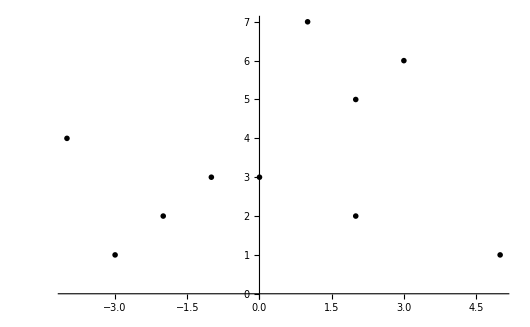

```mathematica
ListPlot[data12,PlotRange->Full,PlotTheme->"Monochrome"]
```

```mathematica
w=Table[RandomReal[{-1/20,1/20}],{i,1,3}]
```

{0.0244729,0.0230448,0.0340448}

```mathematica
a[x_]:=Sign[x.w]
```

```mathematica
a[data1[[1]]]
```

1

```mathematica
a[data2]
```

{1,1,1,-1,1}

```mathematica
Q[w_]:=Sum[HeavisideTheta[ -w.data1[[i]]],{i,1,Length[data1]}]+Sum[HeavisideTheta[1 w.data2[[i]]],{i,1,Length[data2]}]
```

```mathematica
Q[w]
```

4

```mathematica
Q[w1]
```

1

```mathematica
a1[x_]:=Sign[x.w1]
```

```mathematica
a1[data1]
```

{1,-1,1,1,1}

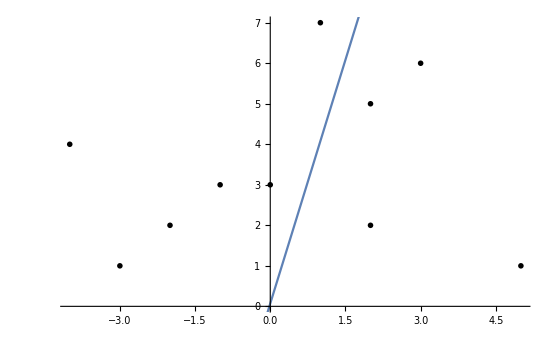

```mathematica
Show[{ListPlot[data12,PlotRange->All,PlotTheme->"Monochrome"],Plot[w1[[1]]x+w1[[2]],{x,-6,6}]}]
```

```mathematica
d1=Table[Module[{i1=RandomReal[{-4,4}]},{i1,-3/4i1+1RandomReal[{-3,1.5}],-1}],{i,1,40}];
```

```mathematica
d2=Table[Module[{i1=RandomReal[{-2,5}]},{i1,-3/4i1+1+RandomReal[{-1,3}],-1}],{i,1,40}];
```

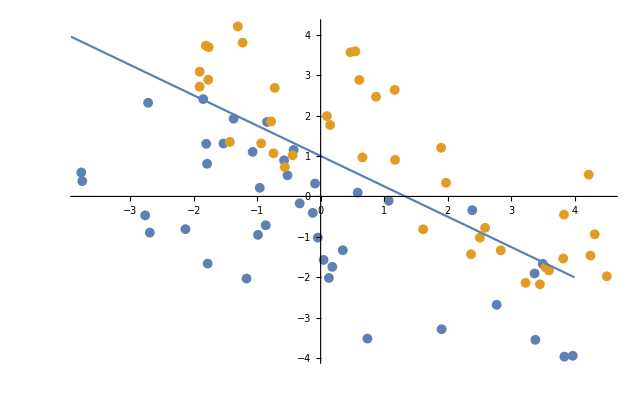

```mathematica
Show[ListPlot[{f@d1,f@d2}],Plot[-3/4x+1,{x,-4,4}]]
```

```mathematica
Q[w_]:=Sum[ArcTan[ -w.d1[[i]]],{i,1,Length[data1]}]+Sum[ArcTan[ w.d2[[i]]],{i,1,Length[data2]}]
```

```mathematica
Q[w1]
```

-12.5664

```mathematica
Sign@Table[w1.d2[[i]],{i,1,Length[d1]}]
```

{-1,-1,-1,-1,-1,-1,-1,-1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1}

```mathematica
w1=NArgMin[Q[{t1,t2,t3}],{t1,t2,t3}]
```

{-3.04143×10^33,-3.20811×10^33,-7.43843×10^32}

```mathematica
f[x_]:=Table[Drop[x[[i]],-1],{i,1,Length[x]}]
```

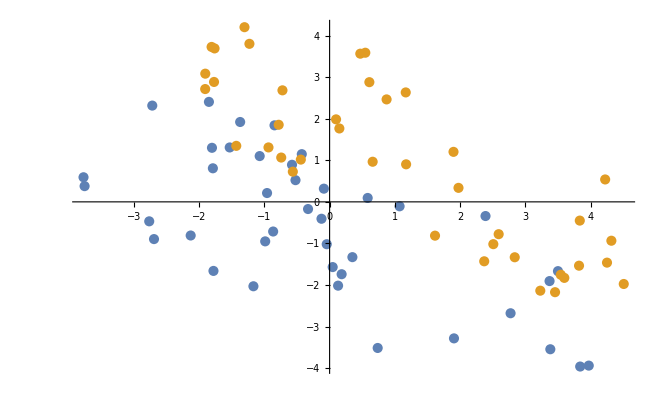

```mathematica
Show[ListPlot[{f[d1],f[d2]}],Plot[w1[[1]]x+w1[[2]],{x,-4,4}]]
```